```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
BB=ΔB/(√3) {{1,0,0},{0,1,0},{0,0,1}};
ϕDD=BB-AA
%//MatrixForm
Print[Style["Tr[ϕDD.ϕDD†]:",Red,16]];
Simplify[Tr[ϕDD.ConjugateTranspose[ϕDD]],Assumptions->{{ΔB,ΔA}∈Reals}]
```

{{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}

(-ΔA/(√2)+ΔB/(√3) | -(ⅈ ΔA)/(√2) | 0
0 | ΔB/(√3) | 0
0 | 0 | ΔB/(√3))

Tr[ϕDD.ϕDD†]:

ΔA^2-√(2/3) ΔA ΔB+ΔB^2

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************)
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(**********************************)
Print[Style[" α Aαi Aαi^* term:",Red,16]]
fα=Simplify[α Tr[Aαi.AαiH],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fαϕ=Collect[%,ϕ]
```

α Aαi Aαi^* term:

α ΔA^2+(α (3 ΔA^2-√6 ΔA ΔB+3 ΔB^2) ϕ^2)/(3 ϕ0^2)+(α ϕ (-6 ΔA^2 ϕ0+√6 ΔA ΔB ϕ0))/(3 ϕ0^2)

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,Δ,αα}∈Reals,D12∈Complexes,D11∈Complexes}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,Δ,αα}∈Reals,D12∈Complexes,D11∈Complexes}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,Δ,αα}∈Reals,D12∈Complexes,D11∈Complexes}];
(**********************************)
Print[Style[" β1 Aαi^* Aαi^* Aβj Aβj term:",Red,16]]
fβ1=FullSimplify[β1 (Tr[AαiC.AαiH]) (Tr[Aαi.AαiT]),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ1ϕ=Collect[%,ϕ]
```

β1 Aαi^* Aαi^* Aβj Aβj term:

(β1 ΔB^2 (6 ΔA^2-6 √6 ΔA ΔB+9 ΔB^2) ϕ^4)/(9 ϕ0^4)+(2 β1 ΔA^2 ΔB^2 ϕ^2)/(3 ϕ0^2)+(β1 ΔB^2 ϕ^3 (-12 ΔA^2 ϕ0+6 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β2 Aαi^* Aαi Aβj^* Aβj term:",Red,16]]
fβ2=FullSimplify[β2 (Tr[AαiC.AαiT]) (Tr[AαiC.AαiT]),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ2ϕ=Collect[%,ϕ]
```

β2 Aαi^* Aαi Aβj^* Aβj term:

β2 ΔA^4+(β2 (9 ΔA^4-6 √6 ΔA^3 ΔB+24 ΔA^2 ΔB^2-6 √6 ΔA ΔB^3+9 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β2 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-48 ΔA^2 ΔB^2 ϕ0+6 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β2 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+24 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β2 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β3 Aαi^* Aβi^* Aαj Aβj term:",Red,16]]
fβ3=FullSimplify[β3 Tr[(AαiC.AαiH).((Aαi.AαiT)ᵀ)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ3ϕ=Collect[%,ϕ]
```

β3 Aαi^* Aβi^* Aαj Aβj term:

(β3 ΔB^2 (9 ΔA^2-2 √6 ΔA ΔB+3 ΔB^2) ϕ^4)/(9 ϕ0^4)+(β3 ΔA^2 ΔB^2 ϕ^2)/ϕ0^2+(β3 ΔB^2 ϕ^3 (-18 ΔA^2 ϕ0+2 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β4 Aαi^* Aβi Aβj^* Aαj term:",Red,16]]
fβ4=FullSimplify[β4 Tr[(AαiC.AαiT).(AαiC.AαiT)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ4ϕ=Collect[fβ4,ϕ]
```

β4 Aαi^* Aβi Aβj^* Aαj term:

β4 ΔA^4+(β4 (9 ΔA^4-6 √6 ΔA^3 ΔB+15 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β4 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-30 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β4 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+15 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β4 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AA,DD,AAT,AAH,AAC,DDT,DDH,Aαi,Aαj,Aβi,Aβj,Aβj1,Aβj2,AαiC,AβiC,AαiC1,AβjC,AαiC2,α,β1,β2,β3,β4,β5,AαiA,AαjA,AβiA,AβjA,AαiAC,AαjAC,AβjAC,AβiAC,Dαi,Dβi,Dαj,Dβj,Dαi,DαiC,DαjC,Dαi,DβjC,DαiC,DβiC,DβjC,D11,D12,D13,D21,D22,D23,D31,D32,D33]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(***************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(***************************************)
Print[Style[" β5 Aαi^* Aβi Aβj Aαj^* term:",Red,16]]
fβ5=FullSimplify[β5 Tr[(AαiC.AαiT).(Aαi.AαiH)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ5ϕ=Collect[fβ5,ϕ]
```

β5 Aαi^* Aβi Aβj Aαj^* term:

β5 ΔA^4+(β5 (9 ΔA^4-6 √6 ΔA^3 ΔB+9 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β5 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-18 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β5 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+9 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β5 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
fϕ=Collect[(fα+fβ1ϕ+fβ2ϕ+fβ3ϕ+fβ4ϕ+fβ5ϕ),ϕ]-(α ΔA^2+β2 ΔA^4+β4 ΔA^4+β5 ΔA^4);
Clear[β1,β2,β3,β4,β5,α,ΔA,ΔB,ϕ,ϕ0]
Print[Style[" pick out the term (coefficient) of O(ϕ^1): ",16,Red]];
Level[fϕ,1][[4]]
Print[Style[" do some factrization: ",Red,16]]
Factor[%%]
FullSimplify[%/.ΔA->√(-α/(2 (β2+β4+β5))),Assumptions->{{β1,β2,β3,β4,β5,α,ΔA,ΔB,ϕ,ϕ0}∈Reals}]
```

pick out the term (coefficient) of O(ϕ^1):

ϕ (-(2 α ΔA^2)/ϕ0+(√(2/3) α ΔA ΔB)/ϕ0+(β2 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β4 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β5 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4))

do some factrization:

-(ΔA (α+2 β2 ΔA^2+2 β4 ΔA^2+2 β5 ΔA^2) (6 ΔA-√6 ΔB) ϕ)/(3 ϕ0)

0

```mathematica
Clear[α,β,βwc1,βwc2,βwc3,βwc4,βwc5,βsc1,βsc2,βsc3,βsc4,βsc5,β1,β2,β3,β4,β5,βA,βB,ϕ,ϕ0,k,c, J,eV,u,m,m3,ms,s,vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c245,Δ2,ΔA,ΔB];
(*βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);*)
ΔA=√(-α/(2 βA))
ΔB=√(-α/(2 βB))
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)
FullSimplify[ϕ0,Assumptions->{{α,βA,βB,β1,β2,β3,β4,β5}∈Reals}]
```

(√(-α/βA))/(√2)

(√(-α/βB))/(√2)

√(-α/(2 βA)-(√(-α/βA) √(-α/βB))/(√6)-α/(2 βB))

√(-(√(-α/βA) √(-α/βB))/(√6)-(α (βA+βB))/(2 βA βB))

8.83076×10^9

1.14039×10^51

1.37864×10^25 √(-(-1+t)/(7.00651×10^99-3.04363×10^99 t))

1.37864×10^25 √(-(-1+t)/(3.50326×10^99+1/3 (7.00651×10^99-2.5826×10^99 t)-6.95396×10^98 t))

√(-(1.90066×10^50 (-1+t))/(7.00651×10^99-3.04363×10^99 t)-(1.90066×10^50 (-1+t))/(3.50326×10^99+1/3 (7.00651×10^99-2.5826×10^99 t)-6.95396×10^98 t)-1.55188×10^50 √(-(-1+t)/(7.00651×10^99-3.04363×10^99 t)) √(-(-1+t)/(3.50326×10^99+1/3 (7.00651×10^99-2.5826×10^99 t)-6.95396×10^98 t)))

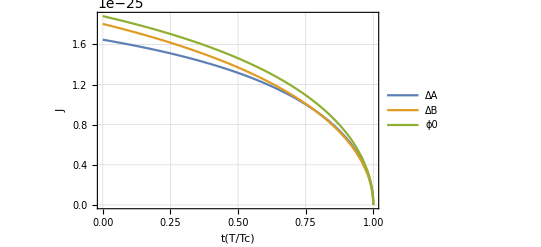

```mathematica
Clear[α,β,βwc1,βwc2,βwc3,βwc4,βwc5,βsc1,βsc2,βsc3,βsc4,βsc5,β1,β2,β3,β4,β5,βA,βB,ϕ,ϕ0,k,c, J,eV,u,m,m3,ms,s,vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c245,Δ2,ΔA,ΔB];
m=1;s=1;J=1;kg=1;k=1;
c=2.99792458 10^8 m s^-1;
hbar=1.054571817 10^-34 J s ;(* plank constant *)
kb=1.380649 10^-23 J k^-1;(**J.K^-1*)
(*π=3.1415926;*)
u= 1.66053906660 10^-27 kg ;
m3=3.016293 u;
(**pressure is 32 bar**)
ms=5.66 m3;
Tc=2.463 10^-3 k^-1;(*mK, kevin*)
vf=32.85 m s^-1;
kf=(vf ms)/hbar
Nf=(ms kf)/(2 π^2 hbar^2)
c1=-0.0402;c2 = -0.1583;c3=-0.0267;c4=-0.3388;c5=-0.3717;
(*******  All βi ********)
βwc1=-(7 Nf Zeta[3])/(240 π^2 kb^2 Tc^2);
βwc2=-2 βwc1;βwc3=-2 βwc1;βwc4=-2 βwc1;βwc5=2 βwc1;
βsc1=c1 Abs[βwc1];βsc2=c2 Abs[βwc1];
βsc3=c3 Abs[βwc1];
βsc4=c4 Abs[βwc1];
βsc5=c5 Abs[βwc1];
β1=βwc1+t βsc1;β2=βwc2+t βsc2;
β3=βwc3+t βsc3;
β4=βwc4+t βsc4;
β5=βwc5+t βsc5;
(***** Gap of A and B - phase *****)
α=1/3 Nf (t-1);
βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);
ΔA=√(-α/(2 βA))
ΔB=√(-α/(2 βB))
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)
Plot[{ΔA,ΔB,ϕ0},{t,0,1},PlotLegends->"Expressions",AxesLabel->{Style["t(T/Tc)",15],Style["J",15]},Frame->True,GridLines->Automatic,PlotRangePadding->Scaled[.1]]
```

Before Plotting the f[ϕ] with ϕDαi = Aαi^B-Aαi^A, let's plot the O(ϕ^1) term: (it must be zero)

0

there is a mathematica bug. If I Fullsimplify O(ϕ^1) before plotting, then it is zero. However, The direct plot of Level[fϕ,1][[4]] isn't show out abusolutely zero but some tiny number 10^-16

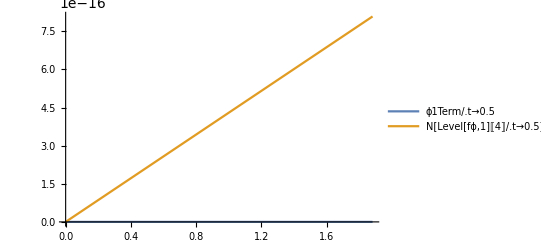

```mathematica
Print[Style[" Before Plotting the f[ϕ] with ϕDαi = Aαi^B-Aαi^A, let's plot the O(ϕ^1) term: (it must be zero)",16,Red ]]
ϕ1Term =FullSimplify[Level[fϕ,1][[4]],Assumptions->{t∈Reals,t>0}]
Print[Style[" there is a mathematica bug. If I Fullsimplify O(ϕ^1) before plotting, then it is zero. However, The direct plot of Level[fϕ,1][[4]] isn't show out abusolutely zero but some tiny number 10^-16 ",16,Red ]]
Plot[{ϕ1Term/.t->0.5,N[(Level[fϕ,1][[4]])/.t->0.5]},{ϕ,0,ϕ0/.t->0.0},PlotLegends->"Expressions"]
```

1.46211×10^-25

-0.137984

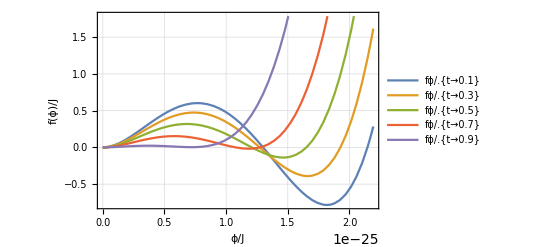

{-8.58993×10^9,-8.58993×10^9,4.29497×10^9,2.14748×10^9,5.36871×10^8}

```mathematica
(********* Plot the f(ϕ) at presure 32 bar **********)
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);
fϕ=ϕ^4 ((β3 ΔB^2 (9 ΔA^2-2 √6 ΔA ΔB+3 ΔB^2))/(9 ϕ0^4)+(β1 ΔB^2 (6 ΔA^2-6 √6 ΔA ΔB+9 ΔB^2))/(9 ϕ0^4)+(β5 (9 ΔA^4-6 √6 ΔA^3 ΔB+9 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4))/(9 ϕ0^4)+(β4 (9 ΔA^4-6 √6 ΔA^3 ΔB+15 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4))/(9 ϕ0^4)+(β2 (9 ΔA^4-6 √6 ΔA^3 ΔB+24 ΔA^2 ΔB^2-6 √6 ΔA ΔB^3+9 ΔB^4))/(9 ϕ0^4))+ϕ^3 ((β3 ΔB^2 (-18 ΔA^2 ϕ0+2 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)+(β1 ΔB^2 (-12 ΔA^2 ϕ0+6 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)+(β4 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-30 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β5 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-18 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β2 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-48 ΔA^2 ΔB^2 ϕ0+6 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4))+ϕ^2 ((α ΔA^2)/ϕ0^2-(√(2/3) α ΔA ΔB)/ϕ0^2+(α ΔB^2)/ϕ0^2+(2 β1 ΔA^2 ΔB^2)/(3 ϕ0^2)+(β3 ΔA^2 ΔB^2)/ϕ0^2+(β5 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+9 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β4 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+15 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+24 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4))+ϕ (-(2 α ΔA^2)/ϕ0+(√(2/3) α ΔA ΔB)/ϕ0+(β2 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β4 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β5 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4));
ϕ0/.t->0.5
fϕ/.{ϕ->(ϕ0/.t->0.5),t->0.5}
Plot[{fϕ/.{t->0.1},fϕ/.{t->0.3},fϕ/.{t->0.5},fϕ/.{t->0.7},fϕ/.{t->0.9}},{ϕ,0,1.5(ϕ0/.t->0.5)},AxesLabel->{Style["ϕ/J",15],Style["f(ϕ)/J",15]},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",PlotRangePadding->{Scaled[.1],Scaled[.05]}]
(*** Plot the coefficient of O(ϕ) ***)
coeffcientϕ=-(2 α ΔA^2)/ϕ0+(√(2/3) α ΔA ΔB)/ϕ0+(β2 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β4 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)+(β5 (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4);
{coeffcientϕ/.{t->0.1},coeffcientϕ/.{t->0.3},coeffcientϕ/.{t->0.5},coeffcientϕ/.{t->0.7},coeffcientϕ/.{t->0.9}}
```